## Setup

```mathematica
Clear[U]
ListNumericQ[L_] := NumericQ[L[[1]]]

TProduct[M__]:=KroneckerProduct[M]
σI = PauliMatrix[0];
σX = PauliMatrix[1];
σY = PauliMatrix[2];
σZ = PauliMatrix[3];

Rx[θ_] := MatrixExp[-ⅈ*θ*σX/2]
Ry[θ_] := MatrixExp[-ⅈ*θ*σY/2]
Rz[θ_] := MatrixExp[-ⅈ*θ*σZ/2]
```

```mathematica
state[θ_, ϕ_] := {Cos[θ/2]*E^(-ⅈ*ϕ/2), Sin[θ/2]*E^(ⅈ*ϕ/2)};
twoQstate[θ1_, ϕ1_, θ2_, ϕ2_]:=Module[{ψ1, ψ2}, (
ψ1 = state[θ1, ϕ1];
ψ2 = state[θ2, ϕ2];
Flatten[TProduct[ψ1, ψ2]]
)]

Clear[stateEntropy]
stateEntropy[ψ_?ListNumericQ] := Module[{ρ, ρA}, (
ρ = TProduct[Conjugate[ψ], ψ];
ρA = ρ[[{1, 2}, {1, 2}]] + ρ[[{3, 4}, {3, 4}]] + .0000000001*{{1, 0}, {0, 1}};

(*Print[ψ];
Print[Limit[-Tr[ρA.MatrixLog[Rationalize[ρA]]/Log[2]], δ->0]];*)

-Tr[ρA.MatrixLog[ρA]/Log[2]] // Chop
)]

Clear[operatorEntropy]
operatorEntropy[U_] := Module[{ψ},
NMaximize[{
stateEntropy[U.twoQstate[θ1, ϕ1, θ2, ϕ2]],
0 ≤ θ1< 2π,
0 ≤ ϕ1< 2π,
0 ≤ θ2< 2π,
0 ≤ ϕ2< 2π
}, {θ1, ϕ1, θ2, ϕ2}
][[1]]
]

(*stateEntropy[twoQstate[1, 2, 3, 4.0]]*)
(*stateEntropy[{0.07304462021810523+0.5237669494328022 ⅈ,-0.06954391031071765-0.39609233445635983 ⅈ,-0.10288009452350523+0.5859609651921747 ⅈ,-0.062488086309299216+0.4480712507558889 ⅈ}]*)
operatorEntropy[{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -ⅈ}}]
```

0.600876

## entropy from ZX interaction

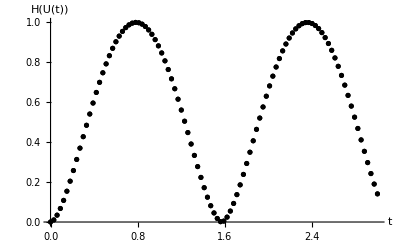

max entropy: 0.999916

```mathematica
H = TProduct[σZ, σZ];
U[t_] := MatrixExp[-ⅈ*t*H]
Tmax = 3;

ts = Table[t, {t, 0, Tmax, Tmax/100}];
entropies = Table[operatorEntropy[U[t]], {t, ts}];
colors = Table[If[perfectEntangler[U[t]], Red, Black], {t, ts}];

ListPlot[{#}&/@Transpose[{ts, entropies}], AxesLabel->{"t", "H(U(t))"}, PlotStyle->colors]
Print["max entropy: " <> ToString[Max[entropies]]]
```

## entropy from ZX interaction with noncommuting term

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

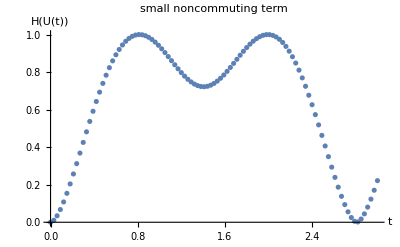

max entropy: 0.999935

```mathematica
H = TProduct[σZ, σZ] + .5*TProduct[σX, σI];
U[t_] := MatrixExp[-ⅈ*t*H]
Tmax = 3;

ts = Table[t, {t, 0, Tmax, Tmax/100}];
entropies = Table[operatorEntropy[U[t]], {t, ts}];

ListPlot[Transpose[{ts, entropies}], PlotLabel->"small noncommuting term", AxesLabel->{"t", "H(U(t))"}]
Print["max entropy: " <> ToString[Max[entropies]]]
```

### Generate gif

```mathematica
gif = Table[Module[{H, Tmax, ts, entropies}, (
Print["computin' " <> ToString[α]];
H = TProduct[σZ, σX] + 100*TProduct[σZ, σI] + α*TProduct[σI, σZ];
U[t_] := MatrixExp[-ⅈ*t*H];
Tmax = 3;

ts = Table[t, {t, 0, Tmax, Tmax/100}];
entropies = Table[operatorEntropy[U[t]], {t, ts}];

Show[
ListPlot[Transpose[{ts, entropies}], PlotLabel->"α = " <> ToString[α], AxesLabel->{"t", "H(U(t))"},PlotRange->{-.1, 1.1}],Graphics[Text[Style["Max entropy: " <> ToString[Max[entropies]],FontSize->12, GrayLevel[0.5]],{1.5, .1}]]
]
(*ListPlot[Transpose[{ts, entropies}], PlotLabel->"α = " <> ToString[α], AxesLabel->{"t", "H(U(t))"}, PlotRange->All]*)
)], {α, {0, .5, .9, 1, 1.1, 2, 5, 10, 100}}];
Export["E:\\entanglementEntropyCR.gif", gif, "AnimationRepetitions"->∞, "DisplayDurations"->2]
(*{0, .1,.3, .6, .9, .95, 1, 1.05, 1.1, 1.3, 1.5, 2, 3, 5, 10, 100}*)
```

computin' 0

computin' 0.5

computin' 0.9

computin' 1

computin' 1.1

computin' 2

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

computin' 5

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

computin' 10

computin' 100

E:\entanglementEntropyCR.gif

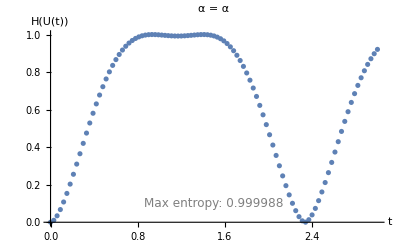

```mathematica
Show[
ListPlot[Transpose[{ts, entropies}], PlotLabel->"α = " <> ToString[α], AxesLabel->{"t", "H(U(t))"},PlotRange->All],Graphics[Text[Style["Max entropy: " <> ToString[Max[entropies]],FontSize->12, GrayLevel[0.5]],{1.5, .1}]]
]
```

```mathematica
Q = 1/Sqrt[2]{{1, 0, 0, ⅈ}, {0, ⅈ, 1, 0}, {0, ⅈ, -1, 0}, {1, 0, 0, -ⅈ}};
m[U_] := Transpose[ConjugateTranspose[Q].U.Q].ConjugateTranspose[Q].U.Q
G1[U_] := Tr[m[U]]^2/(16*Det[U])
G2[U_] := (Tr[m[U]]^2 - Tr[m[U]^2])/(4*Det[U])
G2[DiagonalMatrix[{1, 1, 1, -1}]]
```

1

```mathematica
A = DiagonalMatrix[{1, 1, 1, -1}];
Eigenvalues[A]
(*NSolve[{1 == Cos[c1]^2 Cos[c2]^2 Cos[c3]^2 -  Sin[c1]^2 Sin[c2]^2 Sin[c3]^2 +ⅈ/4 Sin[2c1]Sin[2c2]Sin[2c3],
0 == 4 Cos[c1]^2 Cos[c2]^2 Cos[c3]^2 - 4 Sin[c1]^2 Sin[c2]^2 Sin[c3]^2 - Cos[2c1]Cos[2c2]Cos[2c3]}, {c1, c2, c3}]*)
```

{-1,1,1,1}

```mathematica
Clear[hullContainsZero, perfectEntangler, winding]
winding[poly_,pt_]:=Round[(Total@Mod[(#-RotateRight[#])&@(ArcTan@@(pt-#)&/@poly),2 Pi,-Pi]/2/Pi)]
hullContainsZero[vs_]:=Module[{flag, overallFlag,p1, p2, p3},
(overallFlag = False;
Do[(
p1 ={Re[ss[[1]]], Im[ss[[1]]]};
p2 ={Re[ss[[2]]], Im[ss[[2]]]};
p3 ={Re[ss[[3]]], Im[ss[[3]]]};

If[winding[{p1, p2, p3}, {0, 0}] ≠ 0 || p1 == -p2 || p2 == -p3 || p3 == -p1, overallFlag = True];
), {ss, Subsets[vs, {3}]}];
overallFlag)
]
perfectEntangler[A_] := hullContainsZero[Eigenvalues[m[A]]]
```

```mathematica
TProduct[σX,σX]
```

```mathematica
n = 0;
Do[(
If[perfectEntangler[ⅈ/2 ((a=Table[RandomComplex[],{4},{4}])+ConjugateTranspose[a]) // MatrixExp], n = n + 1];
),{i, 1, 10000}]
n/10000.
```

0.51

```mathematica
XX = TProduct[σX, σX];
YY = TProduct[σY, σY];
ZZ = TProduct[σZ, σZ];
ZX = TProduct[σZ, σX];

XI = TProduct[σX, σI];
YI = TProduct[σY, σI];
ZI = TProduct[σZ, σI];
IX = TProduct[σI, σX];
IY = TProduct[σI, σY];
IZ = TProduct[σI, σZ];
```

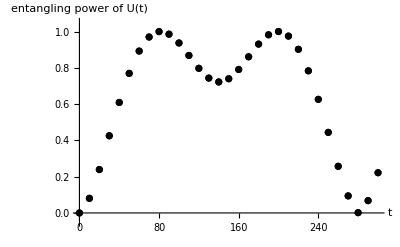

max entropy: 0.999933

```mathematica
H =.01*ZX + {0, 0, 0}.{XI, YI, ZI} + {0, 0, .005}.{IX, IY, IZ};
U[t_] := MatrixExp[-ⅈ*t*H]
Tmax = 300;

ts = Table[t, {t, 0, Tmax, Tmax/30}];
entropies = Table[operatorEntropy[U[t]], {t, ts}];
colors = Table[If[perfectEntangler[U[t]], Red, Black], {t, ts}];

ListPlot[{#}&/@Transpose[{ts, entropies}], AxesLabel->{"t", "entangling power of U(t)"}, PlotStyle->colors, PlotRange->{-.05, 1.05}]
Print["max entropy: " <> ToString[Max[entropies]]]
```

```mathematica
Sqrt[20.^2 - 10^2]
```

17.3205

```mathematica
operatorEntropy[MatrixExp[-ⅈ*(π/4)*ZX]]
```

1.